## Forwards and backwards time

Sketch solutions showing both  t → ∞ and t → -∞.  I start by plotting some approximate numerical solutions in forward time.  I’ll start plotting from t = 0.5 (there is nothing special about this choice of starting time).

### Forward time

ParametricNDSolve::ndsz: At t == 1.69895, step size is effectively zero; singularity or stiff system suspected.

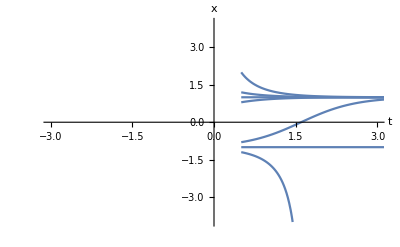

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
delt = 0.2;
plots = {};
f[x_] = 1-x^2;
x0 = {-1-delt, -1, -1+delt, 1-delt, 1,1+delt,2};
  (* set up a six different initial conditions *)
solforward = ParametricNDSolve[{x'[t]==f[x[t]],x[0.5]==xinit},x,{t,0.5,4},xinit,Method->"BDF"];
Do[solx=x[x0[[val]]]/.solforward;
{begintime,endtime} = solx["Domain"][[1]]; 
(* some trajectories diverge, so find the range of time over which the integration worked *)
AppendTo[plots,Plot[solx[t],{t,begintime,endtime},PlotRange->{{0,3},{-4,4}}]],{val,1,Length[x0]}];
(* use that time range over which integration worked to do the plotting *) 
Show[plots,AxesLabel->{t, x},LabelStyle->Medium,PlotRange->{{-3,3},{-4,4}}]
```

### Backwards time

The backwards time system.  t = 0.5 is equivalent to t1 = -0.5, so start this system at time -0.5.  The differential equation has the time reversal.

ParametricNDSolve::ndsz: At t1 == 0.698947, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolve::ndsz: At t1 == 0.0493059, step size is effectively zero; singularity or stiff system suspected.

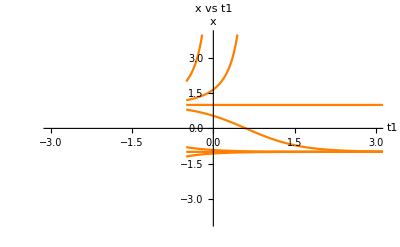

```mathematica
delt = 0.2;
plotnew = {};
solbackward = ParametricNDSolve[{x'[t1]==-f[x[t1]],x[-0.5]==xinit},x,{t1,-0.5,4},xinit,Method->"BDF"];
Do[solx=x[x0[[val]]]/.solbackward;
{begintime,endtime} = solx["Domain"][[1]]; 
AppendTo[plotnew,Plot[solx[t1],{t1,begintime,endtime},PlotRange->{{0,3},{-4,4}},PlotStyle->Orange]];
AppendTo[plots,Plot[solx[-t],{t,-endtime,-begintime},PlotRange->{{0,3},{-4,4}},PlotStyle->Orange]]
(*t1 ∈ [begintime,endtime] is equivalent to t ∈ [-endtime,-begintime].  For example, t1 ∈ [-2,4] is equivalent to t ∈ [-4,2] *),{val,1,Length[x0]}];
Show[plotnew,AxesLabel->{t1, x},PlotRange->{{-3,3},{-4,4}},PlotLabel->"x vs t1"]
```

### Plot solutions x vs t

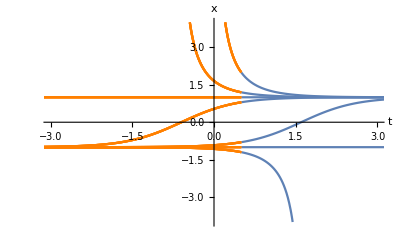

```mathematica
Show[plots,AxesLabel->{t, x},LabelStyle->Medium,PlotRange->{{-3,3},{-4,4}}]
```

The forward time behavior of the solutions is in blue and the backwards time behavior is in orange.  In backwards time, solutions move away from x = 1 and approach x = -1.  In forwards time solutions approach x = 1 and leave x = -1.
Notice that all solution curves are continuous through the starting time (which was t = 0.5 for these simulations).